## Logistic regression (classification)

Logistic regression is a classification method.

In its simplest version, it is designed to classify into two classes, {C_1,C_2}.

Features: Suppose that we have a data set in which instances are characterised by M numerical features: x = {x_1,x_2,...,x_M}

Dependent variable: The class of examples are given by a binary variable y={0,1}  (C_1 for y=0 and C_2 for y=1).

Aim: Given an unseen example with feature vector x', we want to predict the value of y, i.e. the class of the unseen example.

## Example: Menarche as a function of age

### Aim

To motivate the functioning of logistic regression, we address the following problem: Predict whether or not a girl will have had her first period (menarche) at a certain age.

In order to do that, we use data to train a classifier that uses logistic regression as a method.

### The data

Description
The juul data frame has 1339 rows and 6 columns. It contains a reference sample of the distribution of insulin-like growth factor (IGF-I), one observation per subject in various ages, with the bulk of the data collected in connection with school physical examinations.

Format

This data frame contains the following columns:

age - a numeric vector (years).  - Feature x in our analysis

menarche - a numeric vector. Has menarche occurred (code 1: no, 2: yes)? - Dependent variable y

sex -a numeric vector (1: boy, 2: girl).

igf1 - a numeric vector, insulin-like growth factor (microgram per liter).

tanner - a numeric vector, codes 1–5: Stages of puberty ad modum Tanner.

testvol - a numeric vector, testicular volume (ml).

Source
The data contains variables from an investigation performed by Anders Juul (Rigshospitalet, Department for Growth and Reproduction, Denmark)
Presented in the following book:
Peter Dalgaard, "Introductory Statistics with R", 2nd Edition, Springer (2008). 
Data available in the 'ISwR' R package.

### Selecting the feature (age) and dependent variable (menarche)

Download the data juul.dat from MyAberdeen and import it (remember that you can use Insert -> File path... to find the data file in your local directory)

```mathematica
juul=Import["H:\\Teaching\\MSc_Data_Science\\2022-2023_II\\Data\\juul.dat"];
```

```mathematica
Take[juul,10]
```

{{age,menarche,sex,igf1,tanner,testvol},{NA,NA,NA,90,NA,NA},{NA,NA,NA,88,NA,NA},{NA,NA,NA,164,NA,NA},{NA,NA,NA,166,NA,NA},{NA,NA,NA,131,NA,NA},{0.17,NA,1,101,1,NA},{0.17,NA,1,97,1,NA},{0.17,NA,1,106,1,NA},{0.17,NA,1,111,1,NA}}

The data contains the name of features in the heading. I separate the heading from the data:

```mathematica
head=juul[[1]]
```

{age,menarche,sex,igf1,tanner,testvol}

```mathematica
data=Drop[juul,1];
```

#### Dropping missing data

menarche is missing for many individuals (for boys and other for which sex is not available)

We only need rows where data on menarche is available. 

Missing values are indicated as “NA”. One way to drop individuals for which menarche = “NA” is to 
(i) find the position (row) of individuals with  menarche = “NA”
(ii) select the complement of these positions.

```mathematica
posmenarche=Complement[Range[Length[data]],Flatten[Position[data[[All,2]],"NA"]]];
```

We then build a new list that contains {age,menarche}:

```mathematica
dataAM=Transpose[{data[[posmenarche,1]],data[[posmenarche,2]]-1}];
```

```mathematica
dataAM//Length
```

704

```mathematica
dataAM
```

{{8.96,0},{13.01,0},{2.64,0},{5.12,0},{5.68,0},{5.76,0},{5.82,0},{5.82,0},{5.87,0},{5.91,0},{5.92,0},{6,0},{6,0},{6,0},{6,0},{6,0},{6,0},{6,0},{6,0},{6.02,0},{6.06,0},{6.09,0},{6.14,0},{6.17,0},{6.18,0},{6.2,0},{6.2,0},{6.21,0},{6.22,0},{6.23,0},{6.25,0},{6.31,0},{6.32,0},{6.35,0},{6.35,0},{6.35,0},{6.39,0},{6.46,0},{6.47,0},{6.48,0},{6.6,0},{6.6,0},{6.61,0},{6.62,0},{6.67,0},{6.69,0},{6.69,0},{6.69,0},{6.72,0},{6.73,0},{6.74,0},{6.74,0},{6.77,0},{6.78,0},{6.79,0},{6.8,0},{6.8,0},{6.81,0},{6.81,0},{6.83,0},{6.84,0},{6.84,0},{6.86,0},{6.86,0},{6.89,0},{6.92,0},{6.92,0},{6.98,0},{6.99,0},{6.99,0},{7,0},{7.02,0},{7.03,0},{7.03,0},{7.03,0},{7.06,0},{7.1,0},{7.12,0},{7.14,0},{7.14,0},{7.15,0},{7.17,0},{7.2,0},{7.2,0},{7.25,0},{7.26,0},{7.47,0},{7.55,0},{7.55,0},{7.57,0},{7.58,0},{7.62,0},{7.62,0},{7.62,0},{7.62,0},{7.65,0},{7.65,0},{7.68,0},{7.68,0},{7.68,0},{7.69,0},{7.71,0},{7.72,0},{7.78,0},{7.82,0},{7.84,0},{7.86,0},{7.9,0},{7.9,0},{7.95,0},{7.96,0},{7.97,0},{7.99,0},{8,0},{8.03,0},{8.08,0},{8.13,0},{8.17,0},{8.18,0},{8.22,0},{8.29,0},{8.31,0},{8.31,0},{8.34,0},{8.38,0},{8.38,0},{8.42,0},{8.45,0},{8.48,0},{8.5,0},{8.51,0},{8.53,0},{8.53,0},{8.54,0},{8.55,0},{8.56,0},{8.57,0},{8.58,0},{8.58,0},{8.62,0},{8.64,0},{8.66,0},{8.68,0},{8.69,0},{8.7,0},{8.7,0},{8.71,0},{8.75,0},{8.79,0},{8.79,0},{8.81,0},{8.84,0},{8.85,0},{8.87,0},{8.87,0},{8.88,0},{8.9,0},{8.91,0},{8.92,0},{8.94,0},{8.95,0},{8.99,0},{9.01,0},{9.01,0},{9.06,0},{9.06,0},{9.08,0},{9.16,0},{9.19,0},{9.2,0},{9.23,0},{9.23,0},{9.25,0},{9.26,0},{9.28,0},{9.3,0},{9.32,0},{9.32,0},{9.33,0},{9.38,0},{9.4,0},{9.45,0},{9.45,0},{9.46,0},{9.48,0},{9.48,0},{9.49,0},{9.49,0},{9.52,0},{9.56,0},{9.57,0},{9.59,0},{9.67,0},{9.71,0},{9.71,0},{9.76,0},{9.77,0},{9.79,0},{9.8,0},{9.81,0},{9.82,0},{9.82,0},{9.86,0},{9.87,0},{9.89,0},{9.89,0},{9.91,0},{9.94,0},{9.95,0},{9.96,0},{9.97,0},{9.98,0},{9.99,0},{10.01,0},{10.03,0},{10.04,0},{10.09,0},{10.14,0},{10.2,0},{10.2,0},{10.23,0},{10.27,0},{10.27,0},{10.27,0},{10.29,0},{10.33,0},{10.35,0},{10.37,0},{10.37,0},{10.41,0},{10.42,0},{10.42,0},{10.44,0},{10.47,0},{10.48,0},{10.51,0},{10.52,0},{10.55,0},{10.55,0},{10.55,0},{10.57,0},{10.6,0},{10.61,0},{10.62,0},{10.63,0},{10.64,0},{10.69,0},{10.7,0},{10.7,0},{10.73,0},{10.75,0},{10.76,0},{10.76,0},{10.76,0},{10.78,0},{10.78,0},{10.79,0},{10.8,0},{10.87,0},{10.87,0},{10.94,0},{10.95,0},{10.96,0},{10.97,0},{11.03,0},{11.06,0},{11.08,0},{11.08,0},{11.09,0},{11.12,0},{11.13,0},{11.15,0},{11.2,0},{11.23,1},{11.23,0},{11.27,0},{11.29,0},{11.31,0},{11.39,0},{11.41,0},{11.43,0},{11.5,0},{11.51,0},{11.53,0},{11.54,0},{11.55,0},{11.55,1},{11.57,0},{11.59,0},{11.6,0},{11.63,0},{11.69,1},{11.7,0},{11.7,0},{11.73,0},{11.78,0},{11.79,0},{11.82,0},{11.82,0},{11.82,0},{11.82,0},{11.84,0},{11.84,0},{11.84,0},{11.85,0},{11.87,0},{11.88,1},{11.88,0},{11.91,0},{11.91,0},{11.91,0},{11.93,0},{11.95,0},{11.96,0},{12.01,1},{12.01,1},{12.02,0},{12.04,0},{12.05,0},{12.12,0},{12.16,1},{12.17,0},{12.2,1},{12.21,0},{12.23,0},{12.24,1},{12.32,0},{12.32,0},{12.33,1},{12.35,0},{12.36,0},{12.4,0},{12.42,1},{12.45,0},{12.48,0},{12.49,0},{12.49,0},{12.53,0},{12.54,1},{12.56,0},{12.56,0},{12.59,1},{12.6,1},{12.63,0},{12.65,0},{12.68,0},{12.71,0},{12.73,1},{12.75,1},{12.8,0},{12.81,1},{12.82,0},{12.82,0},{12.83,1},{12.84,0},{12.84,1},{12.84,1},{12.85,1},{12.85,0},{12.87,0},{12.88,1},{12.9,1},{12.92,0},{12.93,1},{12.93,1},{12.95,0},{12.99,0},{13.07,0},{13.1,0},{13.1,1},{13.12,1},{13.17,1},{13.25,1},{13.28,0},{13.3,1},{13.31,0},{13.31,1},{13.32,0},{13.32,0},{13.36,0},{13.36,0},{13.41,1},{13.42,1},{13.43,0},{13.54,1},{13.54,1},{13.56,0},{13.58,1},{13.61,1},{13.64,0},{13.65,0},{13.67,0},{13.69,1},{13.69,1},{13.71,1},{13.74,0},{13.75,1},{13.75,0},{13.75,0},{13.81,0},{13.82,1},{13.82,0},{13.86,0},{13.88,0},{13.88,0},{13.89,1},{13.91,1},{13.94,1},{14.01,1},{14.02,0},{14.03,0},{14.06,1},{14.09,1},{14.12,1},{14.15,1},{14.17,1},{14.19,1},{14.22,1},{14.23,1},{14.31,0},{14.39,1},{14.4,1},{14.43,1},{14.44,1},{14.46,1},{14.47,1},{14.48,1},{14.52,1},{14.54,1},{14.56,1},{14.59,1},{14.6,1},{14.69,1},{14.7,1},{14.7,0},{14.72,1},{14.76,1},{14.76,1},{14.8,1},{14.81,1},{14.84,1},{14.84,1},{14.88,1},{14.9,1},{14.93,1},{14.93,0},{14.96,1},{14.97,1},{14.97,1},{15.01,1},{15.07,1},{15.07,1},{15.07,1},{15.09,1},{15.1,1},{15.15,1},{15.17,1},{15.18,1},{15.26,1},{15.37,1},{15.38,1},{15.41,1},{15.44,1},{15.49,1},{15.53,1},{15.55,1},{15.56,1},{15.6,1},{15.7,1},{15.72,1},{15.73,1},{15.79,1},{15.81,1},{15.81,1},{15.84,1},{15.86,1},{15.86,1},{15.88,1},{15.89,1},{16,1},{16.02,1},{16.02,1},{16.03,1},{16.03,1},{16.05,1},{16.13,1},{16.14,1},{16.21,1},{16.24,1},{16.25,1},{16.25,1},{16.27,1},{16.34,1},{16.36,1},{16.38,1},{16.38,1},{16.4,1},{16.41,1},{16.44,1},{16.44,1},{16.48,1},{16.48,1},{16.49,1},{16.5,1},{16.5,1},{16.53,1},{16.57,1},{16.58,1},{16.58,1},{16.62,1},{16.62,1},{16.64,1},{16.64,1},{16.65,1},{16.66,1},{16.67,1},{16.68,1},{16.71,1},{16.74,1},{16.79,1},{16.79,1},{16.84,1},{16.84,1},{16.87,1},{16.89,1},{16.93,1},{16.97,1},{16.97,1},{16.97,1},{16.97,1},{16.99,1},{17.01,1},{17.02,1},{17.03,1},{17.09,1},{17.13,1},{17.13,1},{17.13,1},{17.14,1},{17.15,1},{17.17,1},{17.17,1},{17.17,1},{17.17,1},{17.2,1},{17.21,1},{17.22,1},{17.22,1},{17.23,1},{17.26,1},{17.3,1},{17.3,1},{17.36,1},{17.36,1},{17.37,1},{17.38,1},{17.39,1},{17.39,1},{17.4,1},{17.42,1},{17.45,1},{17.46,1},{17.48,1},{17.49,1},{17.5,1},{17.5,1},{17.5,1},{17.51,1},{17.58,1},{17.58,1},{17.62,1},{17.63,1},{17.64,1},{17.65,1},{17.66,1},{17.71,1},{17.83,1},{17.89,1},{17.94,1},{17.94,1},{17.97,1},{17.98,1},{17.99,1},{17.99,1},{18,1},{18.01,1},{18.03,1},{18.05,1},{18.08,1},{18.09,1},{18.09,1},{18.14,1},{18.17,1},{18.21,1},{18.23,1},{18.24,1},{18.26,1},{18.28,1},{18.32,1},{18.33,1},{18.39,1},{18.4,1},{18.41,1},{18.44,1},{18.47,1},{18.47,1},{18.51,1},{18.55,1},{18.58,1},{18.62,1},{18.64,1},{18.66,1},{18.66,1},{18.68,1},{18.73,1},{18.77,1},{18.77,1},{18.8,1},{18.82,1},{18.83,1},{18.94,1},{18.96,1},{19.02,1},{19.11,1},{19.25,1},{19.35,1},{19.42,1},{19.42,1},{19.48,1},{19.56,1},{19.75,1},{20.78,1},{20.78,1},{21,1},{21.33,0},{22.43,1},{22.8,1},{24,1},{25,1},{25,1},{25.25,1},{25.52,1},{26,1},{26.37,1},{27.59,1},{28,1},{28,1},{29,1},{29,1},{29,1},{30,1},{30,1},{30,1},{30,1},{30,1},{30,1},{31,1},{31,1},{31,1},{31,1},{32.24,1},{34.17,1},{34.54,1},{34.94,1},{34.97,1},{35.16,1},{35.25,1},{35.5,1},{36,1},{36,1},{37,1},{37.28,1},{38,1},{39,1},{40.08,1},{40.91,1},{41,1},{41.43,1},{41.91,1},{42,1},{42.69,1},{43.1,1},{43.33,1},{43.8,1},{44.62,1},{45.22,1},{45.28,1},{45.41,1},{47,1},{47.37,1},{48.01,1},{48.34,1},{49.46,1},{51.07,1},{52,1},{53.18,1},{54,1},{54,1},{58.95,1},{60.99,1},{62.73,1},{65,1},{67.88,1},{75.12,1}}

Here, I have modified the menarche variable to take values {0,1} which are more intuitive for non-menarche and menarche classes.

```mathematica
Take[dataAM,10]
```

{{8.96,0},{13.01,0},{2.64,0},{5.12,0},{5.68,0},{5.76,0},{5.82,0},{5.82,0},{5.87,0},{5.91,0}}

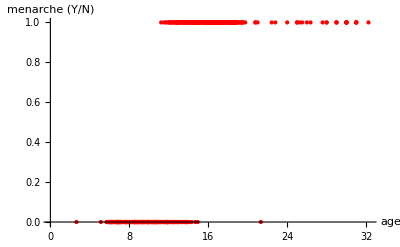

```mathematica
ListPlot[dataAM,PlotStyle->{Red,PointSize[Medium]},AxesLabel->{"age","menarche (Y/N)"}]
```

### Linear regression is not suitable to predict y

Linear regression assumes

y=w_0+w_1 x+ϵ

How does it work here?

```mathematica
pLin=Predict[dataAM[[All,1]]->dataAM[[All,2]],Method->"LinearRegression"]
```

PredictorFunction[…]

```mathematica
plotSDRegion[predictor_,data_,xmin_,xmax_]:=Module[{p=predictor,data0=data,xmin0=xmin,xmax0=xmax,x},
Show[Plot[{p[x],
p[x]+StandardDeviation[p[x,"Distribution"]],p[x]-StandardDeviation[p[x,"Distribution"]]},
{x,xmin0,xmax0},
PlotStyle->{Blue,Gray,Gray},
Filling->{2->{3}},PlotLegends->{"Prediction","Confidence Interval"}],ListPlot[data0,PlotStyle->Red,PlotLegends->{"Data"}]]]
```

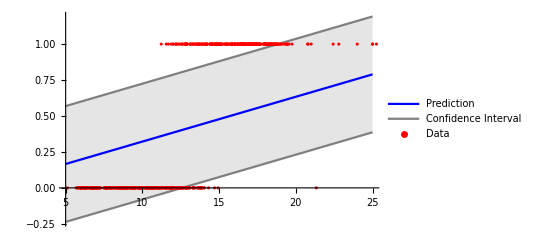

```mathematica
plotSDRegion[pLin,dataAM,5,25]
```

Conclusion: Linear regression does not work well to predict a binary dependent variable y. One should fit a different function!

### Logistic regression assumptions

Logistic regression is based on two basic assumptions:

Since y can take two values (say {0,1}), it is assumed that

y=1 with probability p(x)

y=0 with probability 1-p(x)

A Bernoulli distribution is assumed for y:

y~Ber(p(x))

Note that the probability p depends on the feature x

Typically, a sigmoidal function is used to describe the dependence of p on x. The logistic function is the most widely used:

p(x)=1/(1+e^(-w_0-w_1 x))

The logistic function is already programmed in Wolfram Language. It is the function LogisticSigmoid:

```mathematica
LogisticSigmoid[x]//FunctionExpand
```

1/(1+ⅇ^-x)

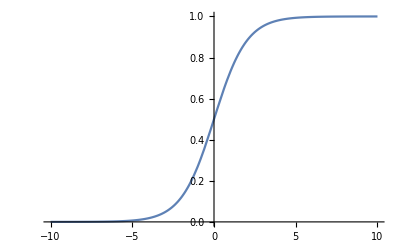

```mathematica
Plot[LogisticSigmoid[x],{x,-10,10}]
```

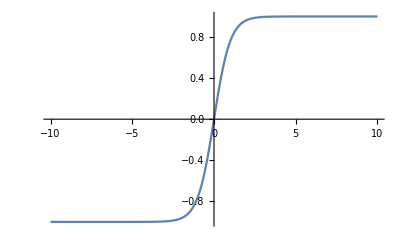

```mathematica
Plot[Tanh[x],{x,-10,10}]
```

#### The logistic function for the menarche problem

By tuning the coefficients w_0 and w_1, one can see that a logistic function can be suitable to describe the data:

```mathematica
Manipulate[Show[Plot[LogisticSigmoid[w0+w1 x],{x,0,35},PlotRange->All,AxesLabel->{"age","menarche (Y/N)"}],ListPlot[dataAM,PlotStyle->{Red,PointSize[Medium]},AxesLabel->{"age","menarche (Y/N)"},PlotRange->{5,30}]],{w0,-40,-5},{w1,0,5}]
```

ListPlot::lpn: dataAM is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in 
    Show[-Graphics-, ListPlot[dataAM, 
      PlotStyle -> {RGBColor[1, 0, 0], PointSize[Medium]}, 
      AxesLabel -> {age, menarche (Y/N)}, PlotRange -> {5, 30}]].

ListPlot::lpn: dataAM is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in 
    Show[-Graphics-, ListPlot[dataAM, 
      PlotStyle -> {RGBColor[1, 0, 0], PointSize[Medium]}, 
      AxesLabel -> {age, menarche (Y/N)}, PlotRange -> {5, 30}]].

ListPlot::lpn: dataAM is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in 
    Show[-Graphics-, ListPlot[dataAM, 
      PlotStyle -> {RGBColor[1, 0, 0], PointSize[Medium]}, 
      AxesLabel -> {age, menarche (Y/N)}, PlotRange -> {5, 30}]].

ListPlot::lpn: dataAM is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in 
    Show[-Graphics-, ListPlot[dataAM, 
      PlotStyle -> {RGBColor[1, 0, 0], PointSize[Medium]}, 
      AxesLabel -> {age, menarche (Y/N)}, PlotRange -> {5, 30}]].

### Using classify to train a logistic regression model

We will now proceed as usual in classification problems. 
(i) Split the data into training and test sets
(ii) Train a classifier using the training dataset
(iii) Test the performance of the classifier using the test dataset

#### Training and test datasets

Select 25% of the rows for training:

```mathematica
ftrain=0.25 Round[Length[dataAM]];
```

```mathematica
ftrain
```

176.

Sort the dataAM randomly to the training and test datasets at random (note that this procedure is slightly different to the way used for the Campylobacter example):

```mathematica
randAM=RandomSample[dataAM];
```

```mathematica
Take[randAM,5]//TableForm
Take[dataAM,5]//TableForm
```

12.35 | 0
8.71 | 0
29 | 1
7.99 | 0
6.06 | 0

8.96 | 0
13.01 | 0
2.64 | 0
5.12 | 0
5.68 | 0

```mathematica
train=randAM[[1;;ftrain]];
test=randAM[[ftrain+1;;Length[randAM]]];
```

Check that the train and test datasets together contain all the examples in dataAM:

```mathematica
Length[train]
Length[test]
Length[randAM]
```

176

528

704

#### Training a classifier

```mathematica
train[[All,1]]-> train[[All,2]]
```

{12.35,8.71,29,7.99,6.06,6.2,18.41,8.57,6.99,6,6.6,16.24,6.74,6.84,17.65,8.08,11.08,12.75,25.25,7.69,11.15,14.47,7.96,14.84,14.09,16.25,17.22,12.42,43.1,14.72,43.33,18.4,7.97,7.17,7.03,11.88,7.86,16.36,17.94,6.21,16.03,21.33,11.84,15.56,14.15,9.38,14.69,13.71,7.47,48.01,14.19,8.38,17.17,13.1,15.53,11.55,6.8,10.37,10.95,6,17.13,8.62,53.18,18.64,10.69,6.74,15.88,11.91,13.69,11.84,8.31,17.99,9.89,14.76,11.43,36,10.76,10.52,6.69,11.82,16.84,49.46,11.93,6.86,7.62,8.18,16.38,29,8.7,18.01,17.5,7.62,7.06,19.02,17.26,11.63,7.65,14.46,34.94,15.37,30,60.99,7.1,9.52,12.17,12.21,6.73,10.33,7.55,18.21,9.8,9.3,12.01,9.59,11.91,32.24,12.4,7.95,7.57,13.1,10.63,16.02,12.71,8.87,15.81,13.86,6.84,6.22,7.03,12.48,18.47,10.62,17.5,8.34,18.55,7.68,9.71,17.98,13.65,13.81,14.03,12.12,9.77,7.65,12.49,17.94,7.68,11.41,13.94,11.7,16.97,12.84,16,9.46,13.88,8.68,6,13.12,16.14,6.83,31,8.66,10.55,15.86,19.42,10.2,44.62,16.41,11.31,12.04,14.23,11.5,5.82,16.79,8.94,18.23}→{0,0,1,0,0,0,1,0,0,0,0,1,0,0,1,0,0,1,1,0,0,1,0,1,1,1,1,1,1,1,1,1,0,0,0,1,0,1,1,0,1,0,0,1,1,0,1,1,0,1,1,0,1,0,1,1,0,0,0,0,1,0,1,1,0,0,1,0,1,0,0,1,0,1,0,1,0,0,0,0,1,1,0,0,0,0,1,1,0,1,1,0,0,1,1,0,0,1,1,1,1,1,0,0,0,0,0,0,0,1,0,0,1,0,0,1,0,0,0,1,0,1,0,0,1,0,0,0,0,0,1,0,1,0,1,0,0,1,0,0,0,0,0,0,0,1,0,0,1,0,1,1,1,0,0,0,0,1,1,0,1,0,0,1,1,0,1,1,0,0,1,0,0,1,0,1}

```mathematica
cLogR=Classify[train[[All,1]]-> train[[All,2]],Method->"LogisticRegression"]
```

ClassifierFunction[…]

```mathematica
Information[cLogR,"Properties"]
```

{Accuracy,BatchEvaluationSpeed,BatchEvaluationTime,Classes,ClassNumber,ClassPriors,EvaluationTime,ExampleNumber,FeatureNames,FeatureNumber,FeatureTypes,Function,FunctionMemory,FunctionProperties,IndeterminateThreshold,L1Regularization,L2Regularization,LearningCurve,MaxTrainingMemory,MeanCrossEntropy,Method,MethodDescription,MethodOption,OptimizationMethod,PerformanceGoal,ProbabilitiesFunction,Properties,TrainingClassPriors,TrainingTime,UtilityFunction}

The probabilities for each class have the expected form for a logistic function:

```mathematica
temp=Information[cLogR,"ProbabilitiesFunction"]
```

Association[{0→0.478527/(0.478527+4.2823×10^-8 ⅇ^(1.21684 #1)),1→1./(1.+1.11746×10^7 ⅇ^(-1.21684 #1))}]&

The function for class y=1 is

```mathematica
temp[x]
```

<|0→0.478527/(0.478527+4.2823×10^-8 ⅇ^(1.21684 x)),1→1./(1.+1.11746×10^7 ⅇ^(-1.21684 x))|>

```mathematica
temp[x][1]
```

1./(1.+1.11746×10^7 ⅇ^(-1.21684 x))

p(x)=1/(1+e^(-w_0-w_1 x))

Mathematica gives the function as 
p(x)=1/(1+a e^-w_1x) where a=e^-w_0. Therefore, w_0=-ln a=-Log[a] .

Fitted coefficients:

```mathematica
w0=-Log[1.1174550473056713*^7]
w1=1.2168389333849723
```

-16.2291

1.21684

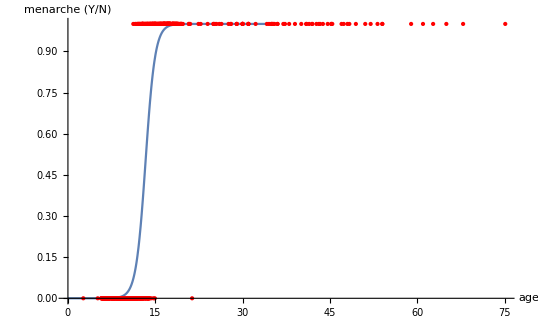

```mathematica
Show[Plot[LogisticSigmoid[w0+w1 x],{x,0,35},PlotRange->All,AxesLabel->{"age","menarche (Y/N)"}],ListPlot[dataAM,PlotRange-> {5,30},PlotStyle->{Red,PointSize[Medium]},AxesLabel->{"age","menarche (Y/N)"}]]
```

#### Probability p(x)=1/2

What is the age at which the probability of menarche is 1/2? This estimates a transition between “unlikely menarche” and “likely menarche”.

p(x)=1/(1+e^(-w_0-w_1 x))=1/2⇒e^(-w_0-w_1 x)=1⇒w_0+w_1 x=0⇒x=-w_0/w_1

```mathematica
-w0/w1
```

13.3371

One can also find a numerical solution for x using the logistic function:

```mathematica
FindRoot[LogisticSigmoid[w0+w1 x]==0.5,{x,15}]
```

{x→13.3371}

Or using the function given by the classifier

```mathematica
FindRoot[temp[x][1]==0.5,{x,15}]
```

{x→13.3371}

### How well does the model fit the data?

#### Comparing to the moving average of observations

We can compare the estimate of the probability of menarche as a function of the age by using moving averages of the data. 

Let us  consider first the fit to the training data, train:

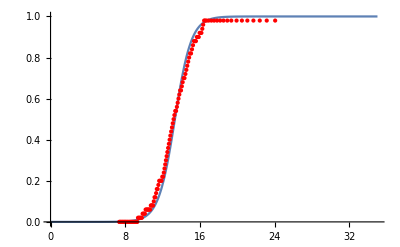

```mathematica
Show[Plot[LogisticSigmoid[w0+w1 x],{x,0,35},PlotRange->All],ListPlot[MovingAverage[Sort[train],50],PlotRange-> {5,30},PlotStyle->{Red,PointSize[Small]},AxesLabel->{"age","menarche (Y/N)"}]]
```

For the test dataset:

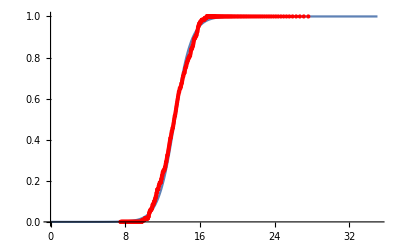

```mathematica
Show[Plot[LogisticSigmoid[w0+w1 x],{x,0,35},PlotRange->All],ListPlot[MovingAverage[Sort[test],120],PlotRange-> {5,30},PlotStyle->{Red,PointSize[Small]},AxesLabel->{"age","menarche (Y/N)"}]]
```

#### Testing with test data

Despite the fact that we only used 25% of the data to train the classifier, it is quite accurate when applied to test data.

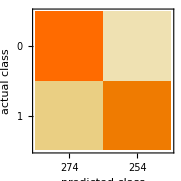
Classifier Measurements
Classifier method | LogisticRegression
Number of test examples | 528
Accuracy | (93.21.1) %
Accuracy baseline | (50.42.2) %
Geometric mean of probabilities | 0.858 ± 0.02
Mean cross entropy | 0.153 ± 0.023
Single evaluation time | 2.43 ms/example
Batch evaluation speed | 57.1 examples/ms
-Graphics- |

```mathematica
cmLogR=ClassifierMeasurements[cLogR,Table[test[[i,1]]->test[[i,2]],{i,1,Length[test]}]]
```

```mathematica
cmLogR["Properties"]
```

{Accuracy,AccuracyBaseline,AccuracyRejectionPlot,AreaUnderROCCurve,BatchEvaluationTime,BestClassifiedExamples,CalibrationCurve,CalibrationData,ClassifierFunction,ClassMeanCrossEntropy,ClassRejectionRate,CohenKappa,ConfusionDistribution,ConfusionFunction,ConfusionMatrix,ConfusionMatrixPlot,CorrectlyClassifiedExamples,DecisionUtilities,Error,EvaluationTime,Examples,F1Score,FalseDiscoveryRate,FalseNegativeExamples,FalseNegativeNumber,FalseNegativeRate,FalsePositiveExamples,FalsePositiveNumber,FalsePositiveRate,GeometricMeanProbability,IndeterminateExamples,LeastCertainExamples,Likelihood,LinearCalibrationCurve,LogLikelihood,MatthewsCorrelationCoefficient,MeanCrossEntropy,MeanDecisionUtility,MisclassifiedExamples,MostCertainExamples,NegativePredictiveValue,Perplexity,Precision,Probabilities,ProbabilityHistogram,Properties,Recall,RejectionRate,Report,ROCCurve,ScottPi,Specificity,TopConfusions,TrueNegativeExamples,TrueNegativeNumber,TruePositiveExamples,TruePositiveNumber,WorstClassifiedExamples}

```mathematica
cmLogR["Accuracy"]
```

0.931818

```mathematica
cmLogR["ConfusionMatrixPlot"]
```

-Graphics-

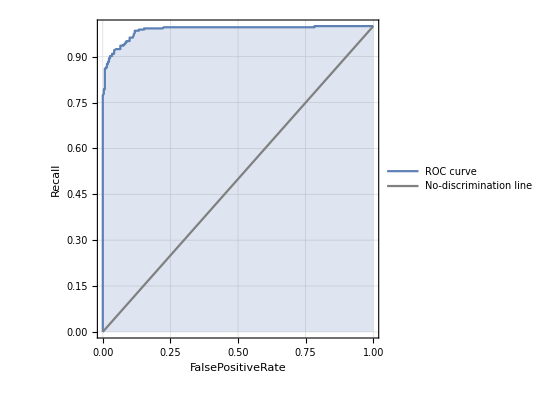
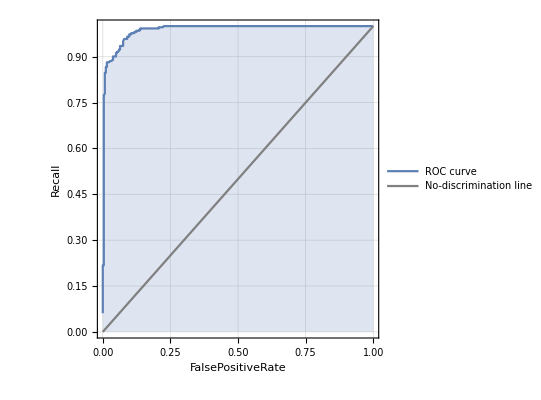
<|0→-Graphics-,1→-Graphics-|>

```mathematica
cmLogR["ROCCurve"]
```

```mathematica
cmLogR["AreaUnderROCCurve"]
```

<|0→0.987143,1→0.987143|>

### Loss (or cost) function - Mean cross-entropy

The classical mean square distance,

J(w_0,w)=1/(2N)∑_(n=1)^N (f(x^(n);w_0,w)-y^(n))^2 ,

used as a cost function for linear regression is not suitable for logistic regression in general (it does not have a single minimum). 

Mean cross-entropy is a more appropriate cost function for logistic regression.

Before introducing the cross-entropy, let us try to understand entropy within the context of probability distributions.

#### Entropy

Within the context of experiments involving randomness, entropy gives an idea of our lack of knowledge about the outcome of experiment. In this context, entropy is a measure of our ignorance about the random outcome.

For example, for most lotteries it is so unlikely to win that we are almost certain that we will not win if we play. The entropy associated with the experiment “play the lottery” is low since we do not ignore much about the outcome - we know that it is very likely not to win.

In contrast, if we toss a fair coin, we are quite uncertain about the outcome: It could be heads or tails with equal probability so it is not easy to predict the outcome.

For a fair six-sided dice, we are even more uncertain since there are more possible outcomes.

In general, if the outcome of an experiment can be defined in terms of a discrete random variable X taking K discrete values {x_1,x_2,...,x_K} with probability distribution {p_1,p_2,..., p_K}, the entropy is defined as

H=-(p_1 Log[p_1]+p_2 Log[p_2]+...+p_K Log[p_K])=-∑_(i=1)^k p_i Log[p_i]

Aside on the logarithm function (denoted as ln x=ln x = log x). In case you don’t know the natural logarithm function very well , it makes sense to look at its behaviour as a function of x on a plot.

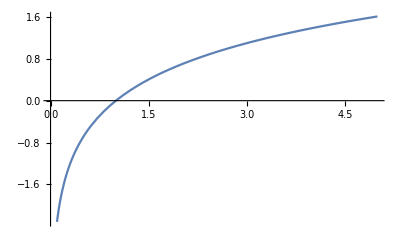

```mathematica
Plot[Log[x],{x,0,5}]
```

Mathematically speaking, the natural logarithm is the inverse of the exponential function e^x since log(e^x)=x

Entropy for the lottery
Two outcomes (win, not win) with probabilities p_win≃0, p_(not win)≃1. 

The entropy is then 

H=-(p_win Log[p_win]+p_(not win)Log[p_(not win)])≃-(0+1×Log[1])=0

So out ignorance about the outcome is low...

Entropy for a coin (not necessarily fair). 
Two outcomes (Heads, Tails) with probabilities p_Heads and p_Tails, respectively.

The entropy is defined as:

H=-(p_Heads Log[p_Heads]+p_Tails Log[p_Tails])=-(p_Heads Log[p_Heads]+(1-p_Heads)Log[1-p_Heads])

Here, I used p_Tails=1-p_Heads.

One can program this with Mathematica:

```mathematica
entropy[p_]:=If[p==0||p==1,0,-(p Log[p]+(1-p) Log[1-p])];
```

```mathematica
pH=0.5;
```

```mathematica
entropy[pH]
```

0.693147

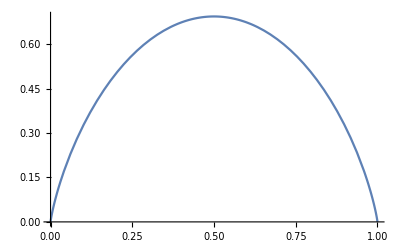

```mathematica
Plot[entropy[p],{p,0,1}]
```

#### Cross-entropy

Consider a training dataset with N examples: D= {{x^(1),y^(1)},{x^(2),y^(2)},...,{x^(N),y^(N)}} where y^(n)∈{0,1} for n=1,2,...,N

In logistic regression, we model an observation for an output variable y^(n) with a probability p(x^(n);w_0,w_1)=1/(1+e^(-w_0-w_1 x^(n))).  The cross-entropy measures our ignorance about the actual observations D when we describe the outcomes with the probability p(x^(n);w_0,w_1).

The cross-entropy is defined in a way that looks similar to the definition of entropy. 

For the n-th example, the cross-entropy is:

CH^(n)=-(y^(n)Log[p(x^(n);w_0,w_1)]+(1-y^(n)) Log(1-p(x^(n);w_0,w_1)))

This quantifies the information lost when the observed probability distribution y^(n) is fitted by the probability p(x^(n);w_0,w_1).

To understand the definition of CH^(n) note, for example, that perfect knowledge of y^(n) in terms of p(x^(n);w_0,w_1), i.e. the case with y^(n)=p(x^(n);w_0,w_1), leads to CH^(n)=0.

The cost function corresponding to the mean cross-entropy over all the examples is then:

J(w_0,w_1)=(∑_(n=1)^N CH^(n))/N

The goal is to find the values of w_0 and w_1 that minimise J(w_0,w_1). 

We have introduced the mean cross-entropy for logistic regression here but one can define it for any other model where observations are described in terms of probabilities. Mean cross-entropy is widely used in machine learning as a loss function.

Wolfram Language gives the mean cross-entropy as follows:

```mathematica
Information[cLogR,"MeanCrossEntropy"]
```

0.210.05

## Generalisation of logistic regression for K classes - Multinomial logistic regression

The logistic regression method can be extended for classification within K classes, {C_(1,)C_2,...,C_K} using M features,  x = {x_1,x_2,...,x_M}

In this case, the probability of the k-th class is 

p_k(x)=(exp(w_0^(k)+w^(k)x))/(∑_(j=1)^K exp(w_0^(j)+w^(j)x)),

where {w_0^(k),w^(k)} are the coefficients to be fitted for the k-th class. In particular,

w^(k)x = ∑_(m=1)^M w_m^(k)x_m .

The function Classify can automatically implement logistic regression for an arbitrary number of classes and features.

As you can see, the proposed expression for the probability in the general case (any number of classes, K) is not formally identical to assumed  for the binary case (K=2). However, both forms can be shown to be equivalent with an appropriate re-parameterization:

 
and 

See a formal derivation in the “Additional materials - Papers, etc.” folder if you are interested. None of these considerations are essential for the assessments of the course.